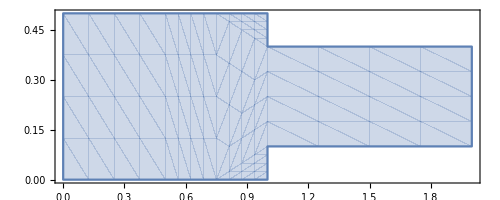

```mathematica
(*Start of given code*)
Ω=RegionUnion[Rectangle[{0,0},{1,1/2}],Rectangle[{1,1/10},{2,2/5}]];
plotΩ=RegionPlot[Ω,AspectRatio->Automatic]
```

```mathematica
op={({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][p][x,y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][p][x,y],Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}/.μ->1;
pde=op=={0,0,0};
bcs={
DirichletCondition[u[x,y]==4*0.3*y*(0.5-y)/(0.41)^2,x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<x<2],
DirichletCondition[p[x,y]==0.,x== 2]};
{xVel,yVel,pressure}=NDSolveValue[{op=={0,0,0},bcs},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.0005}}];
(*End of given code*)
```

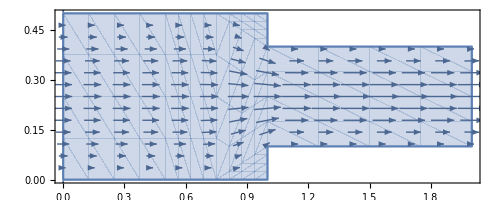

-Graphics3D-

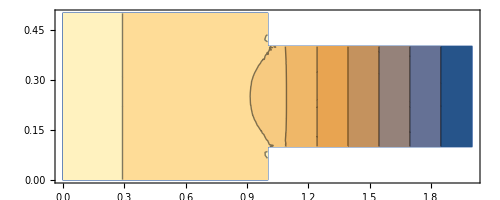

```mathematica
(*The velocity of the fluid*)
Show[plotΩ,VectorPlot[{xVel[x,y], yVel[x,y]},{x,y}∈Ω,PlotLabel->"Velocity of the fluid in Ω"]]

(*The pressure of the fluid*)
Plot3D[pressure[x,y],{x,y}∈Ω,PlotLabel->"Pressure of the fluid in Ω"]
Show[plotΩ,ContourPlot[pressure[x,y],{x,y}∈Ω,PlotLabel->"Pressure of the fluid in Ω"]]
```

```mathematica
d=1;
circleCenter = {10,10};
R=10;
r=1;
minT=0;
maxT=20;
Ω=Disk[circleCenter, R];
NonZeroΩ=Disk[circleCenter, r];
omegaWithT = Cylinder[{Append[circleCenter,minT],Append[circleCenter,maxT]},R];
(*Ensure no transit between Ω and the rest of the plane*)
bondaryCondition = {NeumannValue[0,True]};
(*u0[x,y]:=3 Norm[{x,y}-circleCenter]*)
u0[x,y]:=If[{x,y}∈NonZeroΩ,1,0]
(*{uSol} = NDSolveValue[{-d ∇_{x,y}^2 u[x,y,t]==D[u[x,y,t],t],bondaryCondition},
u,
{x,y,t}∈omegaWithT
(*{x,y}∈Ω,t∈Interval[{0,1}]*)
]*)
(*NDSolveValue[{
∂_t u[x,y,t]-d ∇_{x,y}^2 u[x,y,t]==NeumannValue[0,True],
u[x,y,0]==If[{x,y}∈NonZeroΩ,1,0]},
u,
{t,minT,maxT},
{x,y}∈Ω
]*)
Clear[uSol];
Clear[u];
uSol = NDSolveValue[{
D[u[x,y,t], t]-d ∇_{x,y}^2 u[x,y,t]==NeumannValue[0,True],
(*u[x,y,0]==If[{x,y}∈NonZeroΩ,1,0]*)
u[x,y,0]==u0[x,y]},
u,
{x,y,t}∈omegaWithT
];
Manipulate[
Show[
{ContourPlot[uSol[x,y,t],
{x,0,20},{y,0,20},Contours->15
(*{x,y}∈Ω*)],
VectorPlot[{0,0},{x,0,20},{y,0,20}]
(*VectorPlot[∇_{x,y} uSol[x,y,t],{x,0,20},{y,0,20}]*)
(*VectorPlot[{∂_x uSol[x,y,t],∂_y uSol[x,y,t]},{x,0,20},{y,0,20}]*)
}],
{t,minT,maxT}
]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
(∇_{x,y} uSol[x,y,t]);
D[uSol[x,y,t],x];
D[uSol[x,y,t], x]/.{x->1};
```

{InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][x,y,t],InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][x,y,t]}

InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][x,y,t]

InterpolatingFunction[{{0., 20.}, {0., 20.}, {0., 20.}}, <>][1,y,t]

```mathematica
uf = u[x,y]
ut = uf/.{x->r Cos[θ], y-> r Sin[θ]}
1/r D[(r  D[ut, r]), r] + 1/r^2 D[ut, θ,θ]
(D[uf, x,x] + D[uf, y,y])/.{x->r Cos[θ], y-> r Sin[θ]}
```

u[x,y]

u[r Cos[θ],r Sin[θ]]

1/r^2(-r Sin[θ] u^(0,1)[r Cos[θ],r Sin[θ]]-r Cos[θ] u^(1,0)[r Cos[θ],r Sin[θ]]+r Cos[θ] (r Cos[θ] u^(0,2)[r Cos[θ],r Sin[θ]]-r Sin[θ] u^(1,1)[r Cos[θ],r Sin[θ]])-r Sin[θ] (r Cos[θ] u^(1,1)[r Cos[θ],r Sin[θ]]-r Sin[θ] u^(2,0)[r Cos[θ],r Sin[θ]]))+1/r(Sin[θ] u^(0,1)[r Cos[θ],r Sin[θ]]+Cos[θ] u^(1,0)[r Cos[θ],r Sin[θ]]+r (Sin[θ] (Sin[θ] u^(0,2)[r Cos[θ],r Sin[θ]]+Cos[θ] u^(1,1)[r Cos[θ],r Sin[θ]])+Cos[θ] (Sin[θ] u^(1,1)[r Cos[θ],r Sin[θ]]+Cos[θ] u^(2,0)[r Cos[θ],r Sin[θ]])))

u^(0,2)[r Cos[θ],r Sin[θ]]+u^(2,0)[r Cos[θ],r Sin[θ]]